```mathematica
randomi1 = RandomInteger[{1,2^2}]
randomi2 = RandomInteger[{1,2^3}]
randomi3 = RandomInteger[{1,2^2}]
randomi4 = RandomInteger[{1,2^3}]
randomk = RandomInteger[{1,2^3}]
```

```mathematica
g=NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,0,1}],
{left___,1,0,s___}:>Flatten[{left,s,0,1,0}],
{left___,0,1,s___}:>Flatten[{left,s,1,0}],
{left___,1,1,s___}:>Flatten[{left,s,0,0,0}]

(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi4]]}]*)

(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]*)
}],
{{0,1,1}},
(*{Tuples[{0,1},l][[randomk]]},*)
(*{Tuples[{0,1},l][[k]]},*)
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
```

-Graphics-

```mathematica
allPaths = FindPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]],Infinity,All]
Table[Length /@allPaths[[i]],{i,1,Length[allPaths]}]
Length /@FindPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]],Infinity,All][[3]]
```

{{{0,1,1},{1,1,0},{1,0,1,0},{1,0,0,1,0},{1,0,0,0,1,0},{1,0,0,0,0,1,0}},{{0,1,1},{0,0,0,0},{0,0,0,1},{0,1,0,1},{0,1,1,0},{1,0,1,0},{1,0,0,1,0},{1,0,0,0,1,0},{1,0,0,0,0,1,0}},{{0,1,1},{0,0,0,0},{0,0,0,1},{0,0,1,0},{1,0,0,1},{1,0,1,0},{1,0,0,1,0},{1,0,0,0,1,0},{1,0,0,0,0,1,0}},{{0,1,1},{1,1,0},{0,0,0,0},{0,0,0,1},{0,1,0,1},{0,1,1,0},{1,0,1,0},{1,0,0,1,0},{1,0,0,0,1,0},{1,0,0,0,0,1,0}},{{0,1,1},{1,1,0},{0,0,0,0},{0,0,0,1},{0,0,1,0},{1,0,0,1},{1,0,1,0},{1,0,0,1,0},{1,0,0,0,1,0},{1,0,0,0,0,1,0}}}

{{3,3,4,5,6,7},{3,4,4,4,4,4,5,6,7},{3,4,4,4,4,4,5,6,7},{3,3,4,4,4,4,4,5,6,7},{3,3,4,4,4,4,4,5,6,7}}

{3,4,4,4,4,4,5,6,7}

```mathematica
Length /@FindShortestPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]]]
```

{3,3,4,5,6,7}

```mathematica
AllPathCanyonsBinary[g_]:=Style[Text[
With[
{
vertices=VertexList[g]
(*,randomInit=Tuples[{0,1},2]*)
,allPaths = FindPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]],Infinity,All]
},
(*Length /@FindShortestPath[g,First[VertexList[g]],vertices[[Length[vertices]]]]*)
 Length /@allPaths[[-1]]
]//.{x_}:>x]]

lFn[i1_,i2_,i3_,i4_,j_,k_,l_,t_]:= AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
(*{left___,0,0,s___}:>Flatten[{left,s,0,1}],
{left___,1,0,s___}:>Flatten[{left,s,0,1,0}],
{left___,0,1,s___}:>Flatten[{left,s,1,0}],
{left___,1,1,s___}:>Flatten[{left,s,0,0,0}]*)

(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi4]]}]*)

{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]
}],
(*{{0,1,1}},*)
(*{Tuples[{0,1},l][[randomk]]},*)
{Tuples[{0,1},l][[k]]},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]

Table[Table[Table[Table[Table[Show[
ListStepPlot[
Legended[
lFn[i1,i2,i3,i4,j,k,l,t][[1]][[1]],
StringTemplate[
"{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
(*"a"->{0,1},
"b"->{0,1,0},
"c":>{1,0},
"d":>{0,0,0},
"e":>{0,1,1}*)


(*"a"->Tuples[{0,1},j][[randomi1]],
"b"->Tuples[{0,1},j][[randomi2]],
"c":>Tuples[{0,1},j][[randomi3]],
"d":>Tuples[{0,1},j][[randomi4]],
"e":>Tuples[{0,1},l][[randomk]]*)


"a"->Tuples[{0,1},j][[i1]],
"b"->Tuples[{0,1},j][[i2]],
"c":>Tuples[{0,1},j][[i3]],
"d":>Tuples[{0,1},j][[i4]],
"e":>Tuples[{0,1},l][[k]]
|>]
]]],{t,1,25}],
{i1,1,2^j},
{i2,1,2^j},
{i3,1,2^j},
{i4,1,2^j}],
{j,2,3}],
{k,1,2^l}],
{l,2,3}]/.{{{{{{{x_}}}}}}} -> x
```

Part::partw: Part -1 of {} does not exist.

ListStepPlot::lpn: Integer is not a list of numbers or pairs of numbers.

Show::gtype: ListStepPlot is not a type of graphics.

Part::partw: Part -1 of {} does not exist.

ListStepPlot::lpn: Integer is not a list of numbers or pairs of numbers.

Show::gtype: ListStepPlot is not a type of graphics.

Part::partw: Part -1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListStepPlot::lpn: Integer is not a list of numbers or pairs of numbers.

General::stop: Further output of ListStepPlot::lpn will be suppressed during this calculation.

Show::gtype: ListStepPlot is not a type of graphics.

General::stop: Further output of Show::gtype will be suppressed during this calculation.

$Aborted

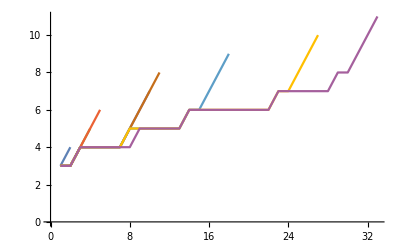

```mathematica
ListLinePlot[Table[Table[Table[Table[Table[
lFn[i1,i2,i3,i4,j,k,l,t][[1]][[1]]
,{t,1,9}],
{i1,2^j,2^j},
{i2,2^j,2^j},
{i3,2^j,2^j},
{i4,2^j,2^j}],
{j,3,3}],
{k,2^l,2^l}],
{l,3,3}]/.{{{{{{{x_}}}}}}} -> x]
```

```mathematica
lFn[i1_,i2_,i3_,i4_,j_,k_,l_,t_]:= AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>{left,s,0,0,1},
{left___,1,0,s___}:>{left,s,0,1,1},
{left___,0,1,s___}:>{left,s,0,1,1},
{left___,1,1,s___}:>{left,s,0,1,1}

(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi4]]}]*)

(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]*)
}],
{{0,1,0}},
(*{Tuples[{0,1},l][[randomk]]},*)
(*{Tuples[{0,1},l][[k]]},*)
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]
```

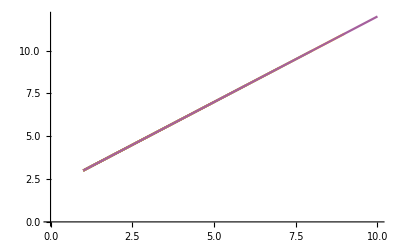

```mathematica
ListLinePlot[Table[Table[Table[Table[Table[
lFn[i1,i2,i3,i4,j,k,l,t][[1]][[1]]
,{t,1,9}],
{i1,2^j,2^j},
{i2,2^j,2^j},
{i3,2^j,2^j},
{i4,2^j,2^j}],
{j,3,3}],
{k,2^l,2^l}],
{l,3,3}]/.{{{{{{{x_}}}}}}} -> x]
```

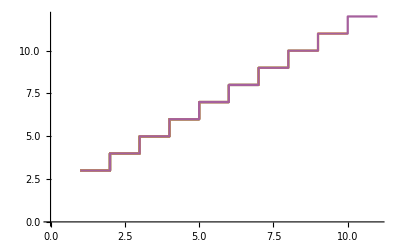

```mathematica
ListStepPlot[Table[Table[Table[Table[Table[
lFn[i1,i2,i3,i4,j,k,l,t][[1]][[1]]
,{t,1,9}],
{i1,2^j,2^j},
{i2,2^j,2^j},
{i3,2^j,2^j},
{i4,2^j,2^j}],
{j,3,3}],
{k,2^l,2^l}],
{l,3,3}]/.{{{{{{{x_}}}}}}} -> x]
```

```mathematica
lFn[r1_,r2_,r3_,r4_,init_,t_]:= AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,r1}],
{left___,1,0,s___}:>Flatten[{left,s,r2}],
{left___,0,1,s___}:>Flatten[{left,s,r3}],
{left___,1,1,s___}:>Flatten[{left,s,r4}]
}],
{init},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]
```

```mathematica
ListStepPlot[Table[Table[Table[Table[Table[
lFn[{0,0,1},{0,1,1},{0,1,1},{0,1,1},{0,1,0},t][[1]][[1]]
,{t,1,9}],
{i1,2^j,2^j},
{i2,2^j,2^j},
{i3,2^j,2^j},
{i4,2^j,2^j}],
{j,3,3}],
{k,2^l,2^l}],
{l,3,3}]/.{{{{{{{x_}}}}}}} -> x]
```

-Graphics-